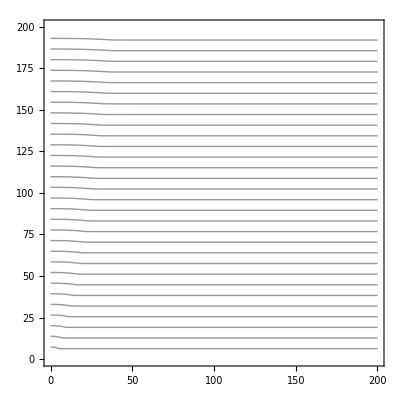

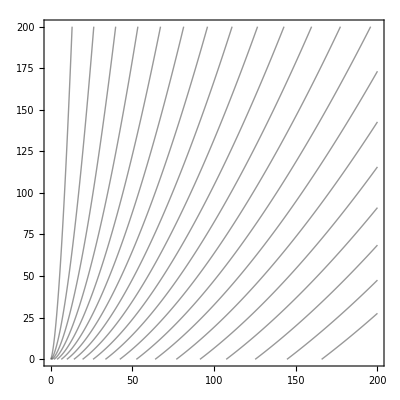

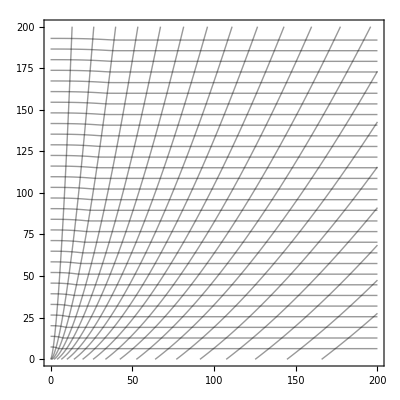

```mathematica
nu = 0.75;
mystep[x_]:=1/Pi ArcTan[x/0.2]+0.5;
(* 1st coordinate is along field lines *)
x1:=r*(Cos[theta])+mystep[1-x2^(2/nu)](1-x2^(2/nu));

(* 2nd coordinate is across field lines 
and equals the sqrt of vector potential 
and changes the sign across the polar axis
(vector potential doesn't change sign across the axis) *)
x2:=r^(nu/2)√2 Cos[theta/2]

(* parameters of the plotting box *)
Rin=0.001;
Rout = 200;
zin = -0.1;
zout = 200;
cpa=ContourPlot[x1//.{r->Sqrt[R^2+z^2],theta->Pi-ArcCos[z/Sqrt[R^2+z^2]]},{R,Rin,Rout},{z,zin,zout},Contours->30,ContourShading->False,PlotPoints->100,DisplayFunction->Identity]
cpb=ContourPlot[x2//.{r->Sqrt[R^2+z^2],theta->Pi-ArcCos[z/Sqrt[R^2+z^2]]},
{R,Rin,Rout},{z,zin,zout},Contours->20,ContourShading->False,PlotPoints->100,DisplayFunction->Identity]
Show[cpa,cpb,DisplayFunction->$DisplayFunction]
```